# Introduction

This notebook is supplementary to preprint https://arxiv.org/abs/2205.01121 and its sole aim is to verify that decomposition of the Toffoli gates presented there are exact. Here we simply import the corresponding quantum circuits and verify the compilation using Mathematica’s algebraic machinery. For context see the original paper.

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

# 3q Toffoli

## Connected

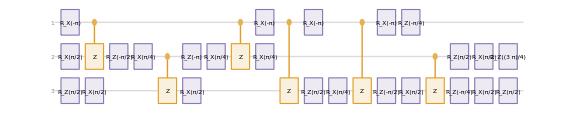

```mathematica
qasm="OPENQASM 2.0;\ninclude \"qelib1.inc\";\nqreg q[3];\nrx(-pi) q[0];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrz(-pi/2) q[1];\nrx(pi/4) q[1];\nrz(pi/2) q[2];\nrx(pi/2) q[2];\ncz q[1],q[2];\nrz(-pi) q[1];\nrx(pi/4) q[1];\ncz q[0],q[1];\nrx(-pi) q[0];\nrx(pi/4) q[1];\nrx(pi/2) q[2];\ncz q[0],q[2];\nrx(-pi) q[0];\nrz(pi/2) q[2];\nrx(pi/4) q[2];\ncz q[0],q[2];\nrx(-pi) q[0];\nrz(-pi/4) q[0];\nrz(-pi/2) q[2];\nrx(pi/2) q[2];\ncz q[1],q[2];\nrz(pi/2) q[1];\nrx(pi/2) q[1];\nrz(3*pi/4) q[1];\nrz(-pi/4) q[2];\nrx(pi/2) q[2];\nrz(pi/2) q[2];\n";
circuit=ImportQASMCircuit[qasm]["QuantumCircuit"];
circuit["Diagram",FontSize->6,PlotRangePadding->0,ImageSize->Large]
```

```mathematica
unitary = circuit["MatrixRepresentation"]//Normal;
(-1)^(3/8)unitary//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

## Chain

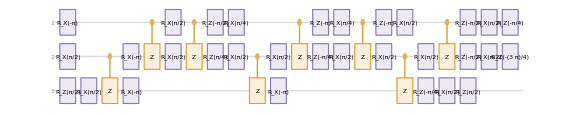

```mathematica
qasm = "OPENQASM 2.0;\ninclude \"qelib1.inc\";\nqreg q[3];\nrx(-pi) q[0];\nrx(pi/2) q[1];\nrz(pi/2) q[2];\nrx(pi/2) q[2];\ncz q[1],q[2];\nrx(-pi) q[1];\ncz q[0],q[1];\nrx(pi/2) q[0];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrz(-pi/2) q[0];\nrx(pi/4) q[0];\nrz(pi/4) q[1];\nrx(pi/2) q[1];\nrx(-pi) q[2];\ncz q[1],q[2];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrz(-pi) q[0];\nrx(pi/4) q[0];\nrz(-pi/4) q[1];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrz(-pi) q[0];\nrx(pi/2) q[0];\nrx(pi/2) q[1];\nrx(-pi) q[2];\ncz q[1],q[2];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrz(-pi/2) q[0];\nrx(pi/2) q[0];\nrz(-pi/4) q[0];\nrz(-pi/2) q[1];\nrx(pi/2) q[1];\nrz(-3*pi/4) q[1];\nrz(-pi/4) q[2];\nrx(pi/2) q[2];\nrz(pi/2) q[2];\n";
circuit=ImportQASMCircuit[qasm]["QuantumCircuit"];
circuit["Diagram",FontSize->6,PlotRangePadding->0,ImageSize->Large]
```

```mathematica
unitary = circuit["MatrixRepresentation"]//Normal;
(-1)^(5/8)unitary//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

# 4q Toffoli

## Star

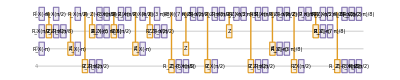

```mathematica
qasm = "OPENQASM 2.0;\ninclude \"qelib1.inc\";\nqreg q[4];\nrx(-pi) q[0];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrx(pi/2) q[0];\nrz(pi/2) q[1];\nrx(pi/8) q[1];\nrx(-pi) q[2];\ncz q[0],q[2];\nrx(pi/2) q[0];\nrx(-pi) q[2];\ncz q[0],q[3];\ncz q[0],q[1];\nrz(-3*pi/8) q[0];\nrx(pi/2) q[0];\nrz(-pi) q[1];\nrx(5*pi/8) q[1];\ncz q[0],q[1];\nrz(-pi) q[0];\nrx(pi/2) q[0];\ncz q[0],q[2];\nrx(pi/2) q[0];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrx(3*pi/8) q[0];\nrz(-pi/2) q[1];\nrx(pi/2) q[1];\nrx(-pi) q[2];\nrz(pi/2) q[3];\nrx(pi/2) q[3];\ncz q[0],q[3];\nrx(7*pi/8) q[0];\ncz q[0],q[2];\nrz(-pi/2) q[0];\nrx(pi/2) q[0];\nrz(-5*pi/8) q[3];\nrx(pi/2) q[3];\ncz q[0],q[3];\nrz(pi/8) q[0];\nrx(pi/2) q[0];\ncz q[0],q[1];\nrz(-pi/2) q[0];\nrx(3*pi/8) q[0];\nrx(pi/2) q[3];\ncz q[0],q[3];\nrz(-pi) q[0];\nrx(pi/8) q[0];\ncz q[0],q[2];\nrz(-pi/2) q[0];\nrx(pi/2) q[0];\nrx(-pi) q[2];\nrz(-3*pi/8) q[2];\nrz(pi/2) q[3];\nrx(pi/2) q[3];\ncz q[0],q[3];\nrz(7*pi/8) q[0];\nrx(pi/2) q[0];\ncz q[0],q[1];\nrz(-pi/2) q[0];\nrx(5*pi/8) q[0];\nrx(-pi) q[1];\nrz(-7*pi/8) q[1];\nrx(pi/2) q[3];\ncz q[0],q[3];\nrz(-pi/2) q[0];\nrx(pi/2) q[0];\nrz(-3*pi/8) q[0];\nrz(-3*pi/8) q[3];\nrx(pi/2) q[3];\nrz(pi/2) q[3];\n";
circuit=ImportQASMCircuit[qasm]["QuantumCircuit"];
circuit["Diagram",FontSize->5,PlotRangePadding->0,ImageSize->Full]
```

```mathematica
unitary = circuit["MatrixRepresentation"]//Normal;
-(-1)^(1/16)unitary//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

# 5q Toffoli

## 4q Toff square root chain topology

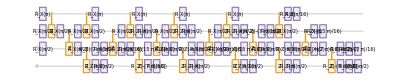

```mathematica
qasm = "OPENQASM 2.0;\ninclude \"qelib1.inc\";\nqreg q[4];\nrx(pi) q[0];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrx(pi/2) q[1];\nrx(pi/2) q[2];\ncz q[1],q[2];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrx(pi) q[0];\nrx(pi/2) q[1];\nrx(pi/2) q[2];\ncz q[2],q[3];\nrz(7*pi/16) q[2];\nrx(pi/2) q[2];\ncz q[1],q[2];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrx(pi) q[0];\nrz(-pi) q[1];\nrx(pi/2) q[1];\nrz(pi/2) q[2];\nrx(pi/16) q[2];\nrz(pi/2) q[3];\nrx(pi/2) q[3];\ncz q[2],q[3];\nrx(15*pi/16) q[2];\ncz q[1],q[2];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrx(pi) q[0];\nrz(pi) q[1];\nrx(pi/2) q[1];\nrz(pi/2) q[2];\nrx(pi/2) q[2];\nrz(-7*pi/16) q[3];\nrx(pi/2) q[3];\ncz q[2],q[3];\nrz(-pi/16) q[2];\nrx(pi/2) q[2];\ncz q[1],q[2];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrx(pi) q[0];\nrz(-pi) q[1];\nrx(pi/2) q[1];\nrz(-pi/2) q[2];\nrx(9*pi/16) q[2];\nrz(-pi) q[3];\nrx(pi/2) q[3];\ncz q[2],q[3];\nrx(15*pi/16) q[2];\ncz q[1],q[2];\nrz(-7*pi/16) q[1];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrx(pi) q[0];\nrz(pi/16) q[0];\nrx(pi/2) q[1];\nrz(pi/2) q[2];\nrx(pi/2) q[2];\nrz(pi/16) q[3];\nrx(pi/2) q[3];\ncz q[2],q[3];\nrz(pi/16) q[2];\nrx(pi/2) q[2];\ncz q[1],q[2];\nrx(pi) q[1];\nrz(-15*pi/16) q[1];\nrz(-pi/2) q[2];\nrx(7*pi/16) q[2];\nrz(pi) q[3];\nrx(pi/2) q[3];\ncz q[2],q[3];\nrz(-pi/2) q[2];\nrx(pi/2) q[2];\nrz(-7*pi/16) q[2];\nrz(-9*pi/16) q[3];\nrx(pi/2) q[3];\nrz(-pi/2) q[3];\n";
circuit = ImportQASMCircuit[qasm]["QuantumCircuit"];
circuit["Diagram", FontSize->5, PlotRangePadding->0, ImageSize->Full]
```

```mathematica
unitary=circuit["MatrixRepresentation"]//Normal;
(-1)^(-7/32)unitary//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2+ⅈ/2 | 1/2-ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2-ⅈ/2 | 1/2+ⅈ/2)

## 4q Toff relative phase chain topology

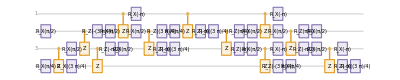

```mathematica
qasm = "OPENQASM 2.0;\ninclude \"qelib1.inc\";\nqreg q[4];\nrx(pi/2) q[1];\nrx(pi/4) q[3];\ncz q[2],q[3];\nrx(pi/2) q[2];\ncz q[1],q[2];\nrz(-3*pi/4) q[1];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrx(-pi) q[0];\nrx(pi/2) q[1];\nrx(3*pi/4) q[3];\ncz q[2],q[3];\nrz(-pi/2) q[2];\nrx(pi/2) q[2];\ncz q[1],q[2];\nrz(3*pi/4) q[1];\nrx(pi/4) q[1];\ncz q[0],q[1];\nrz(-pi) q[1];\nrx(3*pi/4) q[1];\nrz(-pi) q[2];\nrx(3*pi/4) q[2];\ncz q[1],q[2];\nrz(pi/4) q[1];\nrx(pi/2) q[1];\ncz q[0],q[1];\nrx(-pi) q[0];\nrx(pi/2) q[1];\nrz(-pi) q[2];\nrx(pi/2) q[2];\ncz q[2],q[3];\nrx(-pi) q[2];\ncz q[1],q[2];\nrz(pi/4) q[1];\nrx(pi/2) q[1];\nrz(-pi/2) q[2];\nrx(pi/2) q[2];\nrz(-3*pi/4) q[3];\nrx(pi/4) q[3];\ncz q[2],q[3];\nrx(-pi) q[2];\nrz(-pi) q[3];\nrx(3*pi/4) q[3];\n";
circuit = ImportQASMCircuit[qasm]["QuantumCircuit"];
circuit["Diagram", FontSize->5, PlotRangePadding->0, ImageSize->Full]
```

```mathematica
unitary=circuit["MatrixRepresentation"]//Normal;
unitary//FullSimplify//MatrixForm
```

(-(-1)^(3/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(-1)^(1/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (-1)^(3/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (-1)^(1/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1)^(1/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1)^(3/4) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1)^(3/4) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-1)^(1/4) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)